Initialization cell: initializes plot font and colour options so as to not require calling them every time a plot is made.

```mathematica
Needs["HierarchicalClustering`"]
SetOptions[Plot,ImageSize->Medium,PlotStyle->{Black,Thick},BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[MatrixPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[Plot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black}];
SetOptions[ParametricPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->19}];
SetOptions[ListPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black},PlotMarkers->None,Filling->Axis];
```

General Pitchfork bifurcation example: It is known as Pitchfork bifurcation per Strogatz whilst as Saddlenode bifurcation per Roberto Munez Alicea.  Surprisingly, the terminology varies between textbooks.  The prize for naming this type of Bifurcation goes to Abraham and Shaw (1988) for calling it blue sky bifurcation.

f(x,μ) = μ x - x^3describes a pitchfork bifurcation, with μ being the parameter that may be controlled.  Changing μ changes from stable to unstable situations.

Notwithstanding naming convention, μ=0 and μ<0 have stable stationary points (vectors converge to the stationary points) while μ>0 shows instability.  Per Strogatz, the third order term has a stabilizing effect.

{{x→0},{x→-√μ},{x→√μ}}

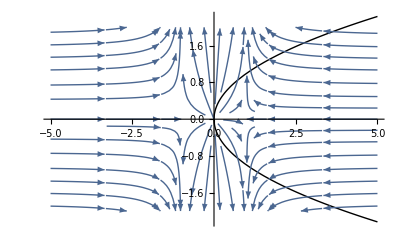

```mathematica
Clear[x,f,μ,y];
f=μ x-x^3;
Solve[f==0,x]
μ=1;
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{√μ,-√μ},{μ,-5,5},PlotStyle->{{Thick,Black},{Thick,Black}}],StreamPlot[{μ x-x^3,y},{x,-5,5},{y,-2,2},GridLines->Automatic,StreamScale->Medium]]
```

For the non linear evolution equation that governs liquid film dynamics (Zero gravity, Marangoni effect, surface tension and porous substrate), the derivative of the growth rate equation (and the growth rate equation itself, as shown in next section) resembles f(x,μ)=μ x - x^3.  For the liquid film, μ=(2 M/(1+Bi)^2 - 2 Pm)/Sn.  Here, Pm is the non-dimensional number governing the strength of porosity, Bi is the Biot number (actually the Nusselt number but Biot number stuck in liquid film dynamics literature), Sn is the surface tension number (have to check but this could be an inverse capillary number or related to it), M is the Marangoni number.  This situation is for zero gravity (The Galileo number, Ga=0).

This demonstrates, supercritical pitchfork bifurcation.  The non-linear (cubic term) has a stabilizing effect (it is the surface tension term) while the value of μ lends stability (μ<0), weak stability (μ=0) and instability (μ>0).  Physically, this can be related to the fact when μ<0, the Permeability term overwhelms thermocapillary instability; μ=0, there is a balance struck between porosity and thermocapillarity or the surface tension term is large enough to reduce μ≈0.  When μ>0, the thermocapillary term has the ability to overwhelm stabilizing porosity.

```mathematica
μ=((2 M)/(Bi+1)^2-2 Pm)/Sn
```

{x→0,x→-√μ,x→√μ}

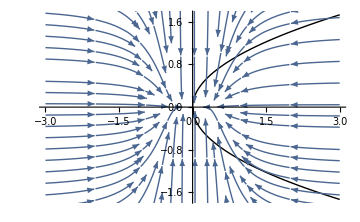

```mathematica
Clear[x,f,μ,y];
f=μ x-(x)^3;
roots=Solve[f==0,x]//Flatten
μ=0;
μmax=If[μ≠ 0,1.5Abs[μ],3];
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-μmax,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,-y},{x,-μmax,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]
]
```

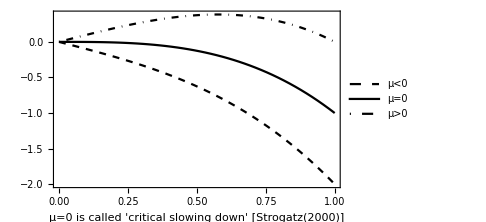

```mathematica
Plot[{-x-x^3,-x^3,x-x^3},{x,0,1},PlotLegends->{"μ<0","μ=0","μ>0"},PlotStyle->{{Dashed,Thick,Black},{Thick,Black},{DotDashed,Thick,Black}},AxesLabel->{"x","f(x,μ)"},Frame->True,FrameLabel->"μ=0 is called 'critical slowing down' [Strogatz(2000)]"]
```

Supercritical bifurcation also exists for the growth rate equation itself (under the constraint of zero gravity, Ga=0.0).  The parameter μ is now given by (1/Sn)(M/(1+Bi)^2-Pm).

0.+(M/(1+Bi)^2-Pm) q-q^3 Sn

{x→0,x→-√μ,x→√μ}

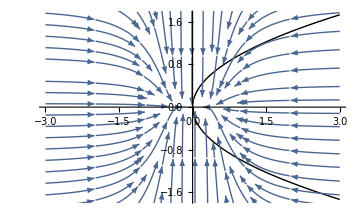

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
Ga=0.;
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;
ff=Collect[f/q,q]

Clear[x,xdot,μ,y];
xdot=μ x-(x)^3;
roots=Solve[xdot==0,x]//Flatten
μ=0;
μmax=If[μ≠ 0,1.5Abs[μ],3];
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-μmax,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,-y},{x,-μmax,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]
]
```

Pendant drop formation due to competition between gravity and surface tension.   Both the growth rate and the fastest growing wavenumber show a subcritical pitchfork bifurcation.

{q→0,q→-(ⅈ √Ga)/(√2 √Sn),q→(ⅈ √Ga)/(√2 √Sn)}

The stationary points are:

{0,-(ⅈ √Ga)/(√2 √Sn),(ⅈ √Ga)/(√2 √Sn)}

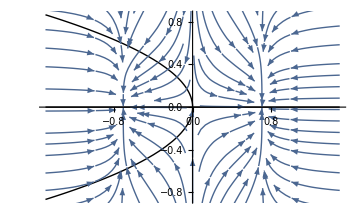

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
Pm=0.;Bi=0.;M=0.;
f=-Ga q^2+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;
df=D[f,q];
roots=Quiet[Solve[df==0,q]]//Flatten
Print["The stationary points are:"]
{roots[[1]][[2]], roots[[2]][[2]], roots[[3]][[2]]}
Ga=-1;
μmax=If[Ga≠ 0,1.5Abs[Ga],3];
Sn=1.;
Show[Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]]},{Ga,-μmax,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{df,-y},{q,-μmax,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]
]
```

Combined case (all physical mechanisms included: surface tension, gravity, thermocapillarity, Porosity).  Biot number, surface tension, thermocapillarity take values as presented in Krishnamoorthy et al. In this case, μ=(1/Sn)(M/(1+Bi)^2-Pm) while λ=(-Pm Ga/Sn).

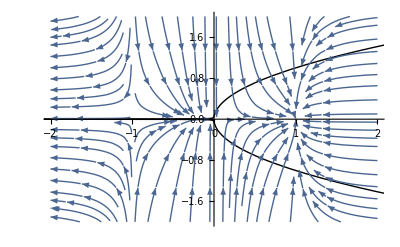

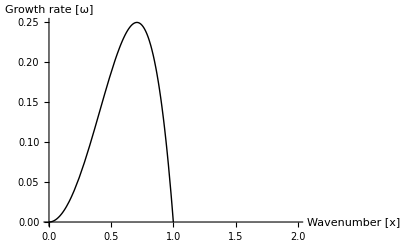

```mathematica
Clear[f,μ,x,λ,roots];
f=μ x^2-x^4 + λ;
roots=Quiet[Solve[f==0,x]]//Flatten;
{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]};
λ=10^-5;
μmin=-5;μmax=5;
xmin=-2;xmax=2;ymin=-2;ymax=2;
Show[
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{μ,μmin,μmax},PlotStyle->{{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},PlotRange->{{xmin,xmax},{ymin,ymax}}],
μ=1;
StreamPlot[{f,-y},{x,xmin,xmax},{y,ymin,ymax},GridLines->Automatic,StreamScale->Medium]
]
Plot[f,{x,0,xmax},PlotStyle->{Thick,Black},AxesLabel->{"Wavenumber [x]","Growth rate [ω]"},PlotRange->{{0,xmax},{0,Automatic}}]
```

Dynamic module that depicts supercritical liquid film bifurcation along with the growth rate of long wave instabilities

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
Bi=0.1;M=5.;S=100.;
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;

roots=Quiet[Solve[f==0,q]]//Flatten;
Ga=0.;Pm=0.025;
Sn=1.;
Collect[f/Sn,q^2];
Collect[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{q^2}];
μmax=If[M≠ 0,Ceiling[0.5Abs[M]],3];
Show[
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{q,-μmax,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{f,-y},{q,-μmax,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]];
```

4.10723 q^2-1. q^4

Krishnamoorthy' s case : Thermocapillary fingering due to a competition between thermocapillarity, surface tension and gravity.  [This and code below are a work in progress.]

0.+3.13223 q^2-100. q^4

{q→-0.176981,q→0.,q→0.,q→0.176981}

{-0.176981,0.,0.,0.176981}

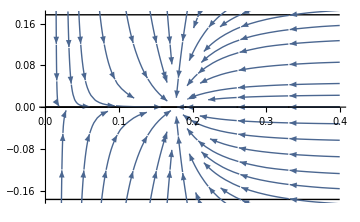

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
Pm=0.;Bi=0.1;Sn=100.;Ga=3;Pm=0.;M=5.;
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn
roots=Quiet[Solve[f==0,q]]//Flatten
{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]}
μmax=0.4;
Show[Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]],roots[[4]][[2]]},{q,0,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{f,-y},{q,0,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]
]
```

8.26446 q-400. q^3

{q→-0.14374,q→0.,q→0.14374}

{-0.14374,0.,0.14374}

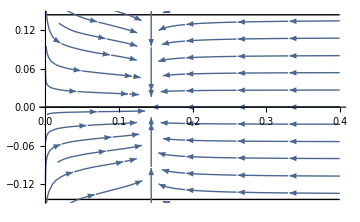

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
Pm=0.;Bi=0.1;Sn=100.;Ga=0;Pm=0.;M=5.;
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;
df=D[f,q]
roots=Quiet[Solve[df==0,q]]//Flatten
{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]]}
μmax=0.4;
Show[Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]]},{q,0,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{df,-y},{q,0,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]
]
```

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm];
Pm=0.;Ga=0.;
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;
df=D[f,q]
roots=Quiet[Solve[df==0,q]]//Flatten
```

(2 M q)/(1+Bi)^2-4 q^3 Sn

{q→0,q→-(√M)/(√2 (1+Bi) √Sn),q→(√M)/(√2 (1+Bi) √Sn)}